```mathematica
nip[i_]=(i*(i-1)*(i-2)*(i-3))/(4!)*3;
np[i_]=(i(i-1)/2);
ratio[i_]=(np[i]+nip[i])/np[i]//N;
ratio[{4,16,28,40}]
```

{1.5,46.5,163.5,352.5}

```mathematica
nip[16]
np[16]
```

5460

120

## Test linear

```mathematica
count=0;
A=3;
For[i=1,i≤A,i++,
For[j=i+1,j≤A,j++,
Print[i,j];
count=count+1
]
]
count
A(A-1)/2
```

12

13

23

3

3

## Test IP quadratic

```mathematica
count=0;
A=4;
For[i=1,i≤A,i++,
For[j=i+1,j≤A,j++,
For[k=1,k≤A,k++,
For[l=k+1,l≤A,l++,
If[k≤i||k==j||l==j,(*Notice the print when false statement*)
count=count,
Print[i,j," ",k,l];
count=count+1
]
]
]
]
]
count
(A(A-1)(A-2)(A-3))/8
```

12 34

13 24

14 23

3

3

## Test fully quadratic

```mathematica
count=0;
A=4;
For[i=1,i≤A,i++,
For[j=i+1,j≤A,j++,
For[k=1,k≤A,k++,
For[l=k+1,l≤A,l++,
If[(k== i&&l==j)||(k== j&&l==i),(*Notice the print when false statement*)
count=count,
Print[i,j," ",k,l];
count=count+1
]
]
]
]
]
count
(A(A-1))/2((A(A-1))/2-1)
```

12 13

12 14

12 23

12 24

12 34

13 12

13 14

13 23

13 24

13 34

14 12

14 13

14 23

14 24

14 34

23 12

23 13

23 14

23 24

23 34

24 12

24 13

24 14

24 23

24 34

34 12

34 13

34 14

34 23

34 24

30

30

## Test fully quadratic without full symmetrization

```mathematica
count=0;
A=5;
For[i=1,i≤A,i++,
For[j=i+1,j≤A,j++,
For[k=1,k≤A,k++,
For[l=k+1,l≤A,l++,
If[(k== i&&l==j)||(k== j&&l==i),(*Notice the print when false statement*)
count=count,
If[k==i||l==j||k==j||l==i,(*non IP check*)
Print[i,j," ",k,l];
count=count+1,
Print[i,j," ",k,l];
count=count+0.5(*Only add half since it will be added again*)
]
]
]
]
]
]
count
(A(A-1))/2((A(A-1))/2-1)-(A(A-1)(A-2)(A-3))/8
```

12 13

12 14

12 15

12 23

12 24

12 25

12 34

12 35

12 45

13 12

13 14

13 15

13 23

13 24

13 25

13 34

13 35

13 45

14 12

14 13

14 15

14 23

14 24

14 25

14 34

14 35

14 45

15 12

15 13

15 14

15 23

15 24

15 25

15 34

15 35

15 45

23 12

23 13

23 14

23 15

23 24

23 25

23 34

23 35

23 45

24 12

24 13

24 14

24 15

24 23

24 25

24 34

24 35

24 45

25 12

25 13

25 14

25 15

25 23

25 24

25 34

25 35

25 45

34 12

34 13

34 14

34 15

34 23

34 24

34 25

34 35

34 45

35 12

35 13

35 14

35 15

35 23

35 24

35 25

35 34

35 45

45 12

45 13

45 14

45 15

45 23

45 24

45 25

45 34

45 35

75.

75

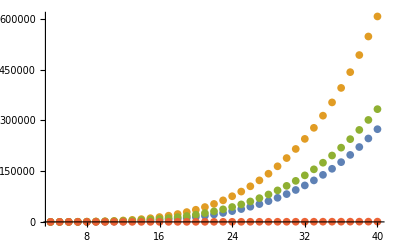

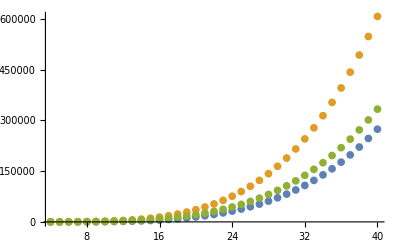

```mathematica
Clear["`*"];
nlin[i_]=(i(i-1))/2;
nip[i_]=(i(i-1)(i-2)(i-3))/8;
nquad[i_]=nlin[i](nlin[i]-1);
nquadfix[i_]=nquad[i]-nip[i];
x=Range[4,40];
ListPlot[{Transpose[{x,nip[x]}],Transpose[{x,nquad[x]}],Transpose[{x,nquadfix[x]}],Transpose[{x,nlin[x]}]},PlotRange->All]
ListPlot[{Transpose[{x,nip[x]}],Transpose[{x,nquad[x]}],Transpose[{x,nquadfix[x]}]},PlotRange->All]
```

```mathematica
x={16,28,40,400};
nquad[x]/nip[x]//N
nquadfix[x]/nip[x]//N
```

{2.61538,2.32,2.21622,2.02015}

{1.61538,1.32,1.21622,1.02015}